```mathematica
H = ({{Δ/2, J}, {J, -Δ/2}});
U =FullSimplify[MatrixExp[-I*t*H]];
U // MatrixForm
```

(Cos[1/2 t √(4 J^2+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2)) | -(2 ⅈ J Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2))
-(2 ⅈ J Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2)) | Cos[1/2 t √(4 J^2+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2)))

```mathematica
FullSimplify[Eigenvalues[H]]
```

{-1/2 √(4 J^2+Δ^2),1/2 √(4 J^2+Δ^2)}

```mathematica
psi0 = {{1},{0}};
psit = FullSimplify[U.psi0] ;
psit // MatrixForm
```

(Cos[1/2 t √(4 J^2+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2))
-(2 ⅈ J Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2)))

```mathematica
populations = FullSimplify[psit * Conjugate[psit], Assumptions->{J>0,Δ>0,t>0}] // Flatten
```

{(2 J^2+Δ^2+2 J^2 Cos[t √(4 J^2+Δ^2)])/(4 J^2+Δ^2),-(2 J^2 (-1+Cos[t √(4 J^2+Δ^2)]))/(4 J^2+Δ^2)}

```mathematica
FullSimplify[Total[populations]]
```

1

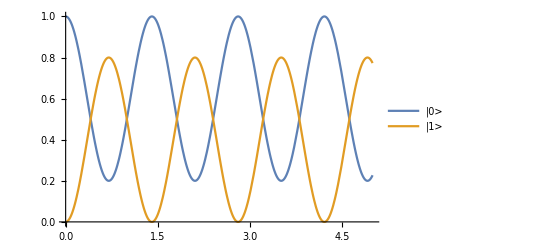

```mathematica
PopulationPlot = populations /.{Δ->2,J->2};
Plot[PopulationPlot,{t, 0, 5}, PlotLegends->{"|0>", "|1>"}]
```

## Matrix Exponential

```mathematica
A = -I*t*H;
Do[Print[MatrixForm[FullSimplify[MatrixPower[A, i]]]], {i,0,5}]
```

(1 | 0
0 | 1)

(-1/2 ⅈ t Δ | -ⅈ J t
-ⅈ J t | (ⅈ t Δ)/2)

(-1/4 t^2 (4 J^2+Δ^2) | 0
0 | -1/4 t^2 (4 J^2+Δ^2))

(1/8 ⅈ t^3 Δ (4 J^2+Δ^2) | 1/4 ⅈ J t^3 (4 J^2+Δ^2)
1/4 ⅈ J t^3 (4 J^2+Δ^2) | -1/8 ⅈ t^3 Δ (4 J^2+Δ^2))

(1/16 t^4 (4 J^2+Δ^2)^2 | 0
0 | 1/16 t^4 (4 J^2+Δ^2)^2)

(-1/32 ⅈ t^5 Δ (4 J^2+Δ^2)^2 | -1/16 ⅈ J t^5 (4 J^2+Δ^2)^2
-1/16 ⅈ J t^5 (4 J^2+Δ^2)^2 | 1/32 ⅈ t^5 Δ (4 J^2+Δ^2)^2)

```mathematica
Series[Cos[x],{x,0,4}]
Series[I*Sin[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

ⅈ x-(ⅈ x^3)/6+O[x]^5

## Eigenvalues

```mathematica
sys = FullSimplify[Eigensystem[H]];
energies = sys[[1]]
modes = sys[[2]]
```

{-1/2 √(4 J^2+Δ^2),1/2 √(4 J^2+Δ^2)}

{{(Δ-√(4 J^2+Δ^2))/(2 J),1},{(Δ+√(4 J^2+Δ^2))/(2 J),1}}

```mathematica
initial = Solve[c1*modes[[1]]+c2*modes[[2]] == psi0,{c1, c2}]
```

{{c1→-J/(√(4 J^2+Δ^2)),c2→J/(√(4 J^2+Δ^2))}}

```mathematica
psit = FullSimplify[(c1 * modes[[1]]*Exp[-I*t*energies[[1]]]+c2*modes[[2]]*Exp[-I*t*energies[[2]]])/.initial];
Transpose[psit]//MatrixForm
```

(Cos[1/2 t √(4 J^2+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2))
-(2 ⅈ J Sin[1/2 t √(4 J^2+Δ^2)])/(√(4 J^2+Δ^2)))